# 6 Feb 2017 NW GaAs mesa 600/100 and 1200/100

```mathematica
path = FileNameJoin[Drop[#,Flatten@{Position[#,"Master"]+1,-1}]&@StringSplit[NotebookDirectory[],"\\"]];
ClearAll[feb6]
feb6=Table[Import[path<>"\\Data\\2017\\feb\\6\\6feb_acuun_"<>ToString[i]<>".dat"],{i,1,20}];
```

```mathematica
ClearAll[allDat,short600100,short1200100,long600100, long1200100,zeros]
short600100 = {"short600100",feb6[[{1,4,5,8,9}]]};
short600100[[2,1,All,3]] = short600100[[2,1,All,3]]+0.33;
short1200100 = {"short1200100",feb6[[{15,16,19}]]};
long600100 = {"long600100",feb6[[{2,3,6,7,10}]]};
long1200100 = {"long1200100",feb6[[{14,17,18}]]};
allDat={short600100,short1200100,long600100, long1200100};
zeros = feb6[[{11,12,20}]];
```

```mathematica
ClearAll[powerDatDict]
powerDatDict = 
<|
"short600100"->{1,0.5,0.29,1.5,2},
"short1200100"->{0.5,1,2},
"long600100"->{1,0.5,0.29,1.5,2},
"long1200100"->{0.5,1,2}
|>;
```

```mathematica
TableForm[Table[Table[allDat[[j]][[2,i]][[1,1]],{i,Length[allDat[[j,2]]]}],{j,Length[allDat]}]]
```

-101.95 | -101.9 | -101.9 | -101.9 | -101.9
-101.95 | -101.95 | -101.95 |  | 
-101.5 | -101.5 | -101.5 | -101.5 | -101.5
-101.5 | -101.5 | -101.5 |  |

#### All measures

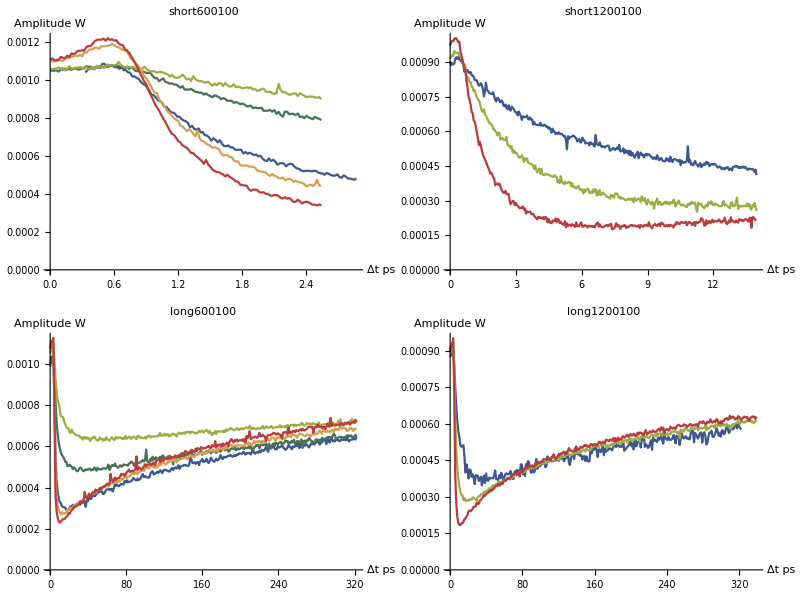

```mathematica
TableForm[
Partition[
Table[
ListLinePlot[
Table[dat[[2,i]][[All,{3,2}]],{i,1,Length[dat[[2]]]}],
ImageSize->450,
AxesLabel->{"Δt ps","Amplitude W"},
PlotLabel->dat[[1]],
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All],
{dat,{short600100,short1200100,long600100, long1200100}}],
2]
]
```

#### Normalization

```mathematica
amplitudes=
Table[
{
dat[[1]],
Table[
MeanFilter[
(dat[[2]][[i,All,2]]+(Max[dat[[2]][[All,1,2]]]-dat[[2]][[i,1,2]]))/Max[dat[[2]][[All,1,2]]],
1],
{i,1,Length[dat[[2]]]}]
},
{dat,{short600100,short1200100,long600100, long1200100}}];
```

```mathematica
normDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat[[i,2]][[j,All,3]],amplitudes[[i,2]][[j]]}],
{j,Length[allDat[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

```mathematica
-normDatDic["short1200100"][[1,1,1]]+normDatDic["short1200100"][[1,2,1]]
```

0.0466993

```mathematica
0.0466993300000948*10^(-12)*10^(15)
```

46.6993

```mathematica
TableForm[
Table[
Rasterize[
ListLinePlot[
normDatDic[name],
ImageSize->600,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{"Δt пс","ΔE_(:0422:0413:0446)/E"},
FrameStyle->Directive[Black, Thick,18],
PlotStyle-> Table[Directive[ColorData["DarkRainbow"][i],AbsoluteThickness[3]],{i,0,1,1/(Length[normDatDic[name]]-1)}],
PlotRange->All,
PlotLegends->(Style["C_(:043f) = "<>ToString[#]<>"×10^15 (:0441:043c)^-3",16]& )/@powerDatDict[name]]
],
{name,{"short600100","short1200100","long600100","long1200100"}}]
]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-

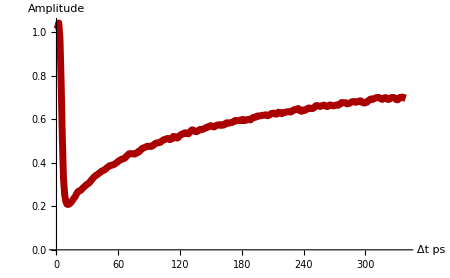

```mathematica
ListLinePlot[
normDatDic["long1200100"][[3]],
ImageSize->450,
AxesLabel->{"Δt ps","Amplitude"},
AxesStyle->Thick,
LabelStyle->{Black,20,Thick},
PlotStyle->{Darker[Red],AbsoluteThickness[5]},

PlotRange->All]
```

#### Logarithmic scaling

```mathematica
normLogDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat[[i,2]][[j,All,3]],Log[amplitudes[[i,2]][[j]]]}],
{j,Length[allDat[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

```mathematica
TableForm[
Table[
Rasterize[
ListLinePlot[
normLogDatDic[name],
ImageSize->600,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{"Δt пс","Log(ΔE_(:0422:0413:0446)/E)"},
FrameStyle->Directive[Black, Thick,18],
PlotStyle-> Table[Directive[ColorData["DarkRainbow"][i],AbsoluteThickness[3]],{i,0,1,1/(Length[normDatDic[name]]-1)}],
PlotRange->All,
PlotLegends->(Style["C_(:043f) = "<>ToString[#]<>"×10^15 (:0441:043c)^-3",16]& )/@powerDatDict[name]]
],
{name,{"short600100","short1200100","long600100","long1200100"}}]
]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-

Short dynamic

#### Short dynamic for mesa 600/100

```mathematica
zerosTimeShift = zeros[[1]][[18,3]]-zeros[[1]][[1,3]];
```

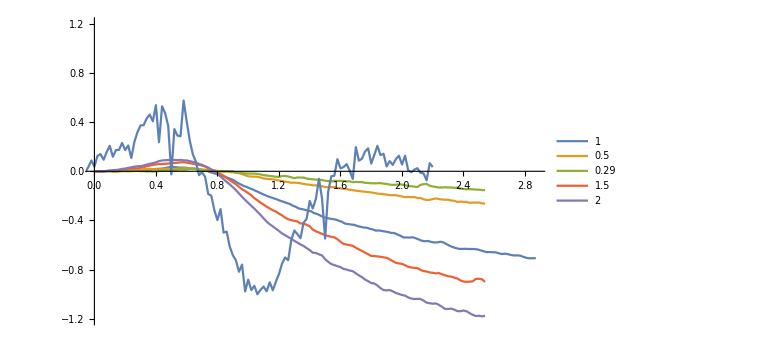

```mathematica
Show[
ListLinePlot[normLogDatDic["short600100"],PlotLegends->powerDatDict["short600100"],ImageSize->Large,PlotRange->{Automatic,{-1.2,1.2}}],
With[{max = Max[Abs[zeros[[2]][[All,2]]]]},ListLinePlot[(zeros[[2]][[All,{3,2}]]/.{x_,y_}->{x-zerosTimeShift,y/max})]]
]
```

Linear area for this mesa

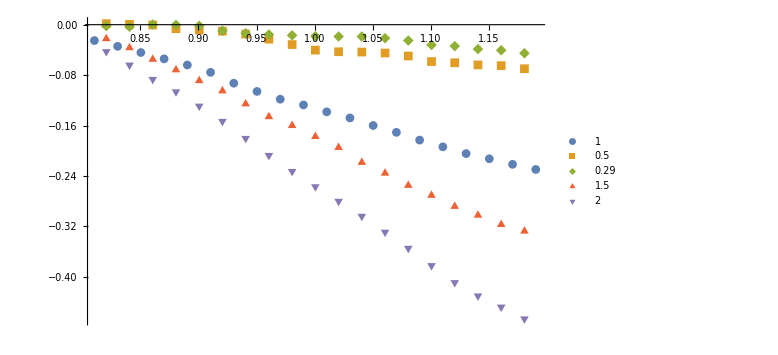

```mathematica
ListPlot[Join[{normLogDatDic["short600100"][[1,25;;44]]},normLogDatDic["short600100"][[2;;,42;;60]]],PlotLegends->powerDatDict["short600100"],ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
lineEreaShort600100 = Join[{normLogDatDic["short600100"][[1,25;;44]]},normLogDatDic["short600100"][[2;;,42;;60]]];
```

```mathematica
lineCoefShort600100 = Table[FindFit[lineEreaShort600100[[i]],a t+b,{a,b},t],{i,1,Length[lineEreaShort600100]}];
```

```mathematica
(Style["C_(:043f) = "<>ToString[#]<>"×10^15 (:0441:043c)^-3",16]& )/@powerDatDict["short600100"]
```

{C_п = 1×10^15 см^-3,C_п = 0.5×10^15 см^-3,C_п = 0.29×10^15 см^-3,C_п = 1.5×10^15 см^-3,C_п = 2×10^15 см^-3}

```mathematica
Rasterize@
Show[
ListPlot[
Table[lineEreaShort600100[[i]],{i,1,5}],
PlotLegends->(Style["C_(:043f) = "<>ToString[#]<>"×10^15 (:0441:043c)^-3",16]& )/@powerDatDict["short600100"],
LabelStyle->18,
PlotMarkers->{Automatic,12},
ImageSize->600,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{"Δt пс","Log(ΔE_(:0422:0413:0446)/E)"},
FrameStyle->Directive[Black, Thick,18],
PlotRange->All
],
Plot[
Table[a x+b/.lineCoefShort600100[[i]],{i,1,5}],
{x,0.82,1.18},
PlotStyle->{Gray,Dashed}
]
]
```

-Graphics-

#### Short dynamic for mesa 1200/100

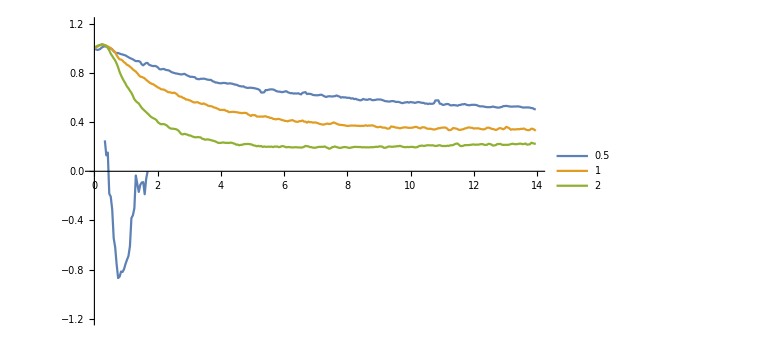

```mathematica
Show[
ListLinePlot[normDatDic["short1200100"],PlotLegends->powerDatDict["short1200100"],ImageSize->Large,PlotRange->{All,{-1.2,1.2}}],
With[{max = Max[Abs[zeros[[2]][[All,2]]]]},ListLinePlot[(zeros[[3]][[All,{3,2}]]/.{x_,y_}->{x+0.33,y/max})]]
]
```

Linear area for this mesa

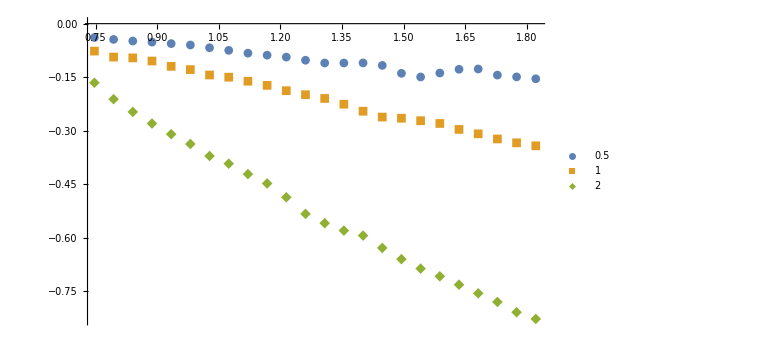

```mathematica
ListPlot[normLogDatDic["short1200100"][[All,17;;40]],PlotLegends->powerDatDict["short1200100"],ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
lineEreaShort1200100 = normLogDatDic["short1200100"][[All,17;;40]];
```

```mathematica
lineCoefShort1200100 = Table[FindFit[lineEreaShort1200100[[i]],a t+b,{a,b},t],{i,1,Length[lineEreaShort1200100]}];
```

```mathematica
Rasterize@
Show[
ListPlot[
Table[lineEreaShort1200100[[i]],{i,1,3}],
PlotLegends->(Style["C_(:043f) = "<>ToString[#]<>"×10^15 (:0441:043c)^-3",16]& )/@powerDatDict["short1200100"],
LabelStyle->18,
PlotMarkers->{Automatic,12},
ImageSize->600,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{"Δt пс","Log(ΔE_(:0422:0413:0446)/E)"},
FrameStyle->Directive[Black, Thick,18],
PlotRange->All
],
Plot[
Table[a x+b/.lineCoefShort1200100[[i]],{i,1,3}],
{x,0.75,1.85},
PlotStyle->{Gray,Dashed}
]
]
```

-Graphics-

#### Short dynamic comparison 1200/100 vs 600/100

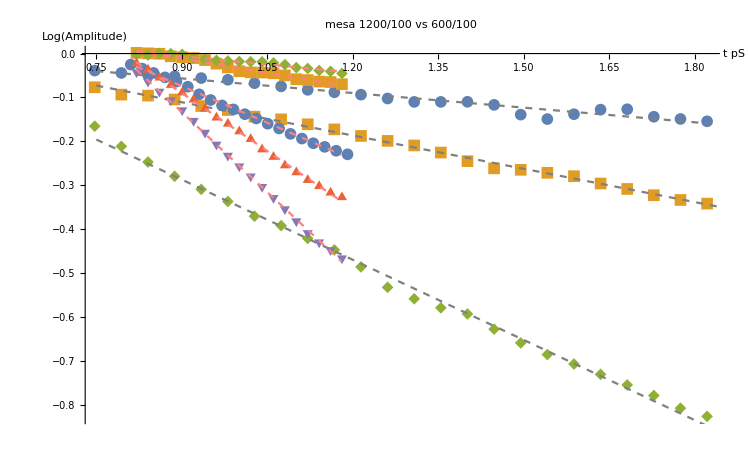

```mathematica
Show[
ListPlot[
Table[lineEreaShort1200100[[i]],{i,1,3}],
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShort1200100[[i]],{i,1,3}],
{x,0.75,1.85},
PlotStyle->{Gray,Dashed}
],
ListPlot[
Table[lineEreaShort600100[[i]],{i,1,5}],
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShort600100[[i]],{i,1,5}],
{x,0.82,1.18},
PlotStyle->{Pink,Dashed}
],
AxesLabel->{"t pS","Log(Amplitude)"},
ImageSize->750,
PlotLabel->"mesa 1200/100 vs 600/100",
LabelStyle->{Black,16}
]
```

```mathematica
Rasterize@
ListPlot[{
Sort[Table[{powerDatDict["short1200100"][[i]],lineCoefShort1200100[[i,1,2]]},{i,1,3}]],Sort[Table[{powerDatDict["short600100"][[i]],lineCoefShort600100[[i,1,2]]},{i,1,5}]],
{{1,-0.034198340663876454},{2,-0.11601286645695738},{4,-0.2861139243939615},{6,-0.44395374361614337}}
},
PlotRange->All,
LabelStyle->{Black,16},
ImageSize->Large,
PlotMarkers->{Automatic,16},
PlotLegends->(Style[#,16]&/@{"a = 1200 нм,  d = 100 нм","a = 600 нм,  d = 100 нм","a = 1200 нм,  d = 65 нм"}),
LabelStyle->18,
PlotMarkers->{Automatic,12},
ImageSize->600,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{"C 10^15(:0441:043c)^-3","-α ТГц"},
FrameStyle->Directive[Black, Thick,18],
PlotRange->All
]
```

-Graphics-

```mathematica
-Mean@Table[
0.067*9.10938356*10^(-31)*13.1*8.85418782*10^(-12)*lineCoefShort1200100[[i,1,2]]*10^12
/
((1.60217662*10^(-19))^2*(powerDatDict["short1200100"][[i]]*10^21)),{i,1,3}]*10^15
-Mean@Table[
0.067*9.10938356*10^(-31)*13.1*8.85418782*10^(-12)*lineCoefShort600100[[i,1,2]]*10^12
/
((1.60217662*10^(-19))^2*(powerDatDict["short600100"][[i]]*10^21)),{i,1,5}]*10^15
-Mean@Table[
0.067*9.10938356*10^(-31)*13.1*8.85418782*10^(-12)*{{1,-0.034198340663876454},{2,-0.11601286645695738},{4,-0.2861139243939615},{6,-0.44395374361614337}}[[i,2]]*10^12
/
((1.60217662*10^(-19))^2*({{1,-0.034198340663876454},{2,-0.11601286645695738},{4,-0.2861139243939615},{6,-0.44395374361614337}}[[i,1]]*10^21)),{i,1,3}]*10^15
```

71.6935

144.174

15.0515

Long dynamic

#### Long dynamic for mesa 600/100

```mathematica
Manipulate[
Row[
Table[
Show[{
ListLinePlot[
normDatDic["long600100"][[i]]
],
Graphics[Line[{{normDatDic["long600100"][[i,<|1->a,2->b,4->c,5-> e|>[i],1]],0},{normDatDic["long600100"][[i,<|1->a,2->b,4-> c,5-> e|>[i],1]],1}}]]
},
PlotRange->{{0,320},{0,1}},
AxesOrigin->{0,0},
LabelStyle->{Black,12},
ImageSize->500,
AxesLabel->{"t pS","Amplitude"},
PlotLabel->"Long dynamic for mesa 600/100 with P_pump="<>ToString[powerDatDict["long600100"][[i]]]<>" mW"],
{i,{2,1,4,5}}
]
],
{a,35,100,1},{b,64,100,1},{c,12,100,1},{e,10,100,1}]
```

ListLinePlot::lpn: long600100 is not a list of numbers or pairs of numbers.

Part::partd: Part specification Missing[KeyAbsent,long600100]⟦2,64,1⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[long600100],},PlotRange→{{0,320},{0,1}},AxesOrigin→{0,0},LabelStyle→{GrayLevel[0],12},ImageSize→500,AxesLabel→{t pS,Amplitude},PlotLabel→Long dynamic for mesa 600/100 with P_pump=long600100 mW].

ListLinePlot::lpn: KeyAbsent is not a list of numbers or pairs of numbers.

Part::partd: Part specification Missing[KeyAbsent,long600100]⟦1,35,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[KeyAbsent],},PlotRange→{{0,320},{0,1}},AxesOrigin→{0,0},LabelStyle→{GrayLevel[0],12},ImageSize→500,AxesLabel→{t pS,Amplitude},PlotLabel→Long dynamic for mesa 600/100 with P_pump=KeyAbsent mW].

Part::partw: Part 4 of Missing[KeyAbsent,long600100] does not exist.

ListLinePlot::lpn: Missing[KeyAbsent,long600100]⟦4⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Part::partw: Part 4 of Missing[KeyAbsent,long600100] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[Missing[KeyAbsent,long600100]⟦4⟧],},PlotRange→{{0,320},{0,1}},AxesOrigin→{0,0},LabelStyle→{GrayLevel[0],12},ImageSize→500,AxesLabel→{t pS,Amplitude},PlotLabel→Long dynamic for mesa 600/100 with P_pump=Missing[KeyAbsent, long600100][[4]] mW].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ListLinePlot::lpn: long600100 is not a list of numbers or pairs of numbers.

Part::partd: Part specification Missing[KeyAbsent,long600100]⟦2,64,1⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[long600100],},PlotRange→{{0,320},{0,1}},AxesOrigin→{0,0},LabelStyle→{GrayLevel[0],12},ImageSize→500,AxesLabel→{t pS,Amplitude},PlotLabel→Long dynamic for mesa 600/100 with P_pump=long600100 mW].

ListLinePlot::lpn: KeyAbsent is not a list of numbers or pairs of numbers.

Part::partd: Part specification Missing[KeyAbsent,long600100]⟦1,35,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[KeyAbsent],},PlotRange→{{0,320},{0,1}},AxesOrigin→{0,0},LabelStyle→{GrayLevel[0],12},ImageSize→500,AxesLabel→{t pS,Amplitude},PlotLabel→Long dynamic for mesa 600/100 with P_pump=KeyAbsent mW].

Part::partw: Part 4 of Missing[KeyAbsent,long600100] does not exist.

ListLinePlot::lpn: Missing[KeyAbsent,long600100]⟦4⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Part::partw: Part 4 of Missing[KeyAbsent,long600100] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[Missing[KeyAbsent,long600100]⟦4⟧],},PlotRange→{{0,320},{0,1}},AxesOrigin→{0,0},LabelStyle→{GrayLevel[0],12},ImageSize→500,AxesLabel→{t pS,Amplitude},PlotLabel→Long dynamic for mesa 600/100 with P_pump=Missing[KeyAbsent, long600100][[4]] mW].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ListLinePlot::lpn: long600100 is not a list of numbers or pairs of numbers.

Part::partd: Part specification Missing[KeyAbsent,long600100]⟦2,64,1⟧ is longer than depth of object.

Part::partw: Part 2 of powerDatDict[long600100] does not exist.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[long600100],},PlotRange→{{0,320},{0,1}},AxesOrigin→{0,0},LabelStyle→{GrayLevel[0],12},ImageSize→500,AxesLabel→{t pS,Amplitude},PlotLabel→Long dynamic for mesa 600/100 with P_pump=powerDatDict[long600100][[2]] mW].

ListLinePlot::lpn: KeyAbsent is not a list of numbers or pairs of numbers.

Part::partd: Part specification Missing[KeyAbsent,long600100]⟦1,35,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[KeyAbsent],},PlotRange→{{0,320},{0,1}},AxesOrigin→{0,0},LabelStyle→{GrayLevel[0],12},ImageSize→500,AxesLabel→{t pS,Amplitude},PlotLabel→Long dynamic for mesa 600/100 with P_pump=long600100 mW].

Part::partw: Part 4 of Missing[KeyAbsent,long600100] does not exist.

ListLinePlot::lpn: Missing[KeyAbsent,long600100]⟦4⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Part::partw: Part 4 of Missing[KeyAbsent,long600100] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[Missing[KeyAbsent,long600100]⟦4⟧],},PlotRange→{{0,320},{0,1}},AxesOrigin→{0,0},LabelStyle→{GrayLevel[0],12},ImageSize→500,AxesLabel→{t pS,Amplitude},PlotLabel→Long dynamic for mesa 600/100 with P_pump=powerDatDict[long600100][[4]] mW].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

```mathematica
initials600100 = <|1->64,2->35,4->12,5->10|>;
```

```mathematica
expr600100 = Hold@((1-normDatDic["long600100"][[i,initials600100[i],2]])*(1-a Exp[-(t-normDatDic["long600100"][[i,initials600100[i],1]])/c]-(1-a) Exp[-(t-normDatDic["long600100"][[i,initials600100[i],1]])/d])+normDatDic["long600100"][[i,initials600100[i],2]]);
```

```mathematica
coef600100 = 
Association[
Table[
{i->
FindFit[
normDatDic["long600100"][[i,initials600100[i];;]],
{ReleaseHold@expr600100},
{a,c,d},t]
},
{i,{1,2,4,5}}
]
];
```

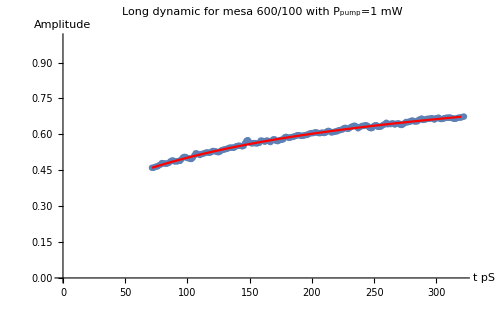
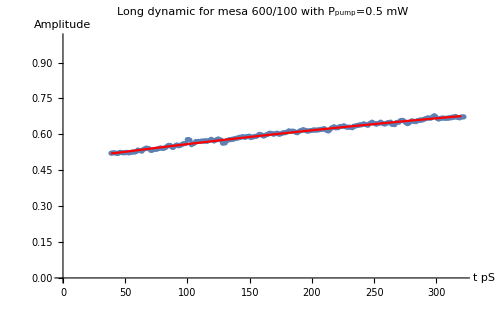
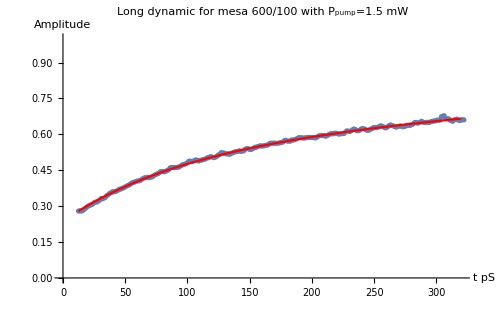
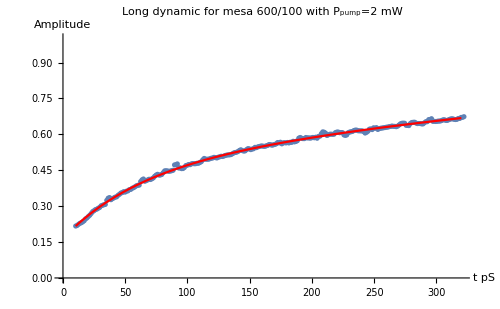

```mathematica
Row[
Table[
Show[
{
ListPlot[
normDatDic["long600100"][[i,initials600100[i];;]]
],
Plot[
(ReleaseHold@expr600100)/.coef600100[i],
{t,normDatDic["long600100"][[i,initials600100[i],1]],320},
PlotStyle->Red
]
},
PlotRange->{{0,320},{0,1}},
AxesOrigin->{0,0},
LabelStyle->{Black,12},
ImageSize->500,
AxesLabel->{"t pS","Amplitude"},
PlotLabel->"Long dynamic for mesa 600/100 with P_pump="<>ToString[powerDatDict["long600100"][[i]]]<>" mW"
],
{i,{1,2,4,5}}
]
]
```

```mathematica
TableForm[Table[{"P = "<>ToString[powerDatDict["long600100"][[k]]],coef600100[k]},{k,Keys[coef600100]}]]
```

P = 1 | a→0.794815
c→822.988
d→99.98
P = 0.5 | a→1.00359
c→711.717
d→1.71712
P = 1.5 | a→0.675351
c→768.677
d→90.5507
P = 2 | a→0.709347
c→596.481
d→59.7715

```mathematica
Rasterize@
Show[
{
ListPlot[
Table[
normDatDic["long600100"][[i,initials600100[i];;]],
{i,{1,2,4,5}}
],
PlotLegends->(Style["C_(:043f) = "<>ToString[#]<>"×10^15 (:0441:043c)^-3",16]& )/@powerDatDict["short600100"][[{1,2,4,5}]],
LabelStyle->18,
PlotMarkers->{Automatic,12},
ImageSize->600,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{"Δt пс","ΔE_(:0422:0413:0446)/E"},
FrameStyle->Directive[Black, Thick,18],
PlotRange->All,
PlotStyle->ColorData[107]
],
Show[
Table[
Plot[
(ReleaseHold@expr600100)/.coef600100[i],
{t,normDatDic["long600100"][[i,initials600100[i],1]],323},
PlotStyle->{Red,AbsoluteThickness[3]}
],
{i,{1,2,4,5}}
]
]}
]
```

-Graphics-

#### Long dynamic for mesa 1200/100

```mathematica
Manipulate[
Row[
Table[
Show[{
ListLinePlot[
normDatDic["long1200100"][[i]]
],
Graphics[Line[{{normDatDic["long1200100"][[i,<|1->a,2->b,3->c|>[i],1]],0},{normDatDic["long1200100"][[i,<|1->a,2->b,3-> c|>[i],1]],1}}]]
},
PlotRange->{{0,320},{0,1}},
AxesOrigin->{0,0},
LabelStyle->{Black,12},
ImageSize->380,
AxesLabel->{"t pS","Amplitude"},
PlotLabel->"Long dynamic for mesa 1200/100 with P_pump="<>ToString[powerDatDict["long1200100"][[i]]]<>" mW"],
{i,3}
]
],
{a,53,100,1},{b,27,100,1},{c,12,100,1}]
```

```mathematica
initials1200100 = <|1->53,2->27,3->12|>;
```

```mathematica
expr1200100 = Hold@((1-normDatDic["long1200100"][[i,initials1200100[i],2]])*(1-a Exp[-(t-normDatDic["long1200100"][[i,initials1200100[i],1]])/c]-(1-a) Exp[-(t-normDatDic["long1200100"][[i,initials1200100[i],1]])/d])+normDatDic["long1200100"][[i,initials1200100[i],2]]);
```

```mathematica
coef1200100 = 
Association[
Table[
{i->
FindFit[
normDatDic["long1200100"][[i,initials1200100[i];;]],
{ReleaseHold@expr1200100},
{a,c,d},t]
},
{i,3}
]
];
```

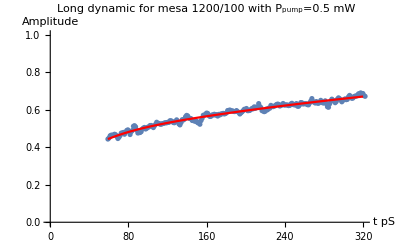
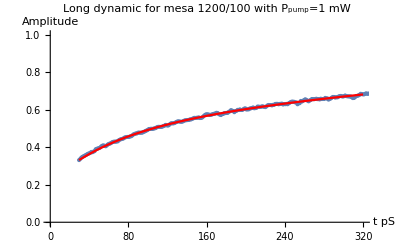
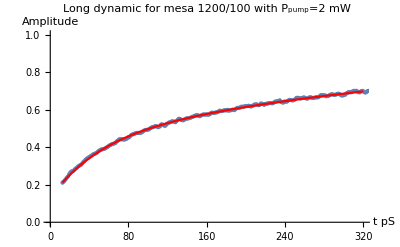

```mathematica
Row[
Table[
Show[
{
ListPlot[
normDatDic["long1200100"][[i,initials1200100[i];;]]
],
Plot[
(ReleaseHold@expr1200100)/.coef1200100[i],
{t,normDatDic["long1200100"][[i,initials1200100[i],1]],320},
PlotStyle->Red
]
},
PlotRange->{{0,320},{0,1}},
AxesOrigin->{0,0},
LabelStyle->{Black,12},
ImageSize->400,
AxesLabel->{"t pS","Amplitude"},
PlotLabel->"Long dynamic for mesa 1200/100 with P_pump="<>ToString[powerDatDict["long1200100"][[i]]]<>" mW"
],
{i,3}
]
]
```

```mathematica
TableForm[Table[{"P = "<>ToString[powerDatDict["long1200100"][[k]]],coef1200100[k]},{k,Keys[coef1200100]}]]
```

P = 0.5 | a→0.922753
c→590.49
d→33.9719
P = 1 | a→0.762561
c→612.275
d→64.7106
P = 2 | a→0.687887
c→525.843
d→50.5201

#### Time comparison

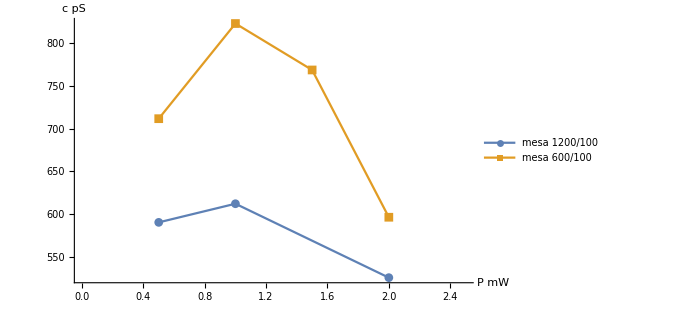

```mathematica
ListLinePlot[
{Sort[Table[{powerDatDict["long1200100"][[k]],coef1200100[k][[2,2]]},{k,Keys[coef1200100]}]],
Sort[Table[{powerDatDict["long600100"][[k]],coef600100[k][[2,2]]},{k,Keys[coef600100]}]]},
PlotMarkers->Automatic,
PlotLegends->{"mesa 1200/100","mesa 600/100"},
ImageSize->500,
AxesLabel->{"P mW","c pS"},
LabelStyle->{Black,14},
PlotRange->{{0,2.5},Automatic},
Mesh->Full
]
```

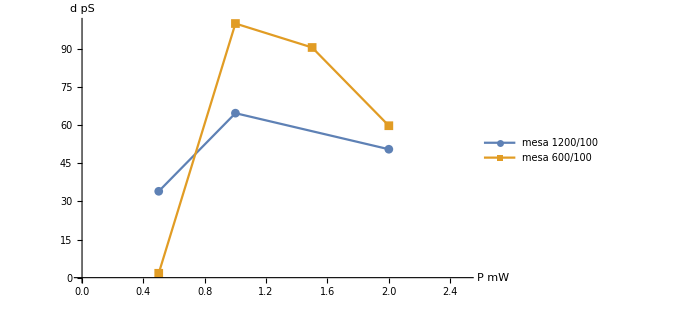

```mathematica
ListLinePlot[
{Sort[Table[{powerDatDict["long1200100"][[k]],coef1200100[k][[3,2]]},{k,Keys[coef1200100]}]],
Sort[Table[{powerDatDict["long600100"][[k]],coef600100[k][[3,2]]},{k,Keys[coef600100]}]]},
PlotMarkers->Automatic,
PlotLegends->{"mesa 1200/100","mesa 600/100"},
ImageSize->500,
AxesLabel->{"P mW","d pS"},
LabelStyle->{Black,14},
PlotRange->{{0,2.5},Automatic},
Mesh->Full
]
```

```mathematica
Rasterize@
Show[
{
ListPlot[
Table[
normDatDic["long1200100"][[i,initials1200100[i];;]],
{i,3}
],
PlotLegends->(Style["C_(:043f) = "<>ToString[#]<>"×10^15 (:0441:043c)^-3",16]& )/@powerDatDict["short1200100"],
LabelStyle->18,
PlotMarkers->{Automatic,12},
ImageSize->600,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{"Δt пс","ΔE_(:0422:0413:0446)/E"},
FrameStyle->Directive[Black, Thick,18],
PlotRange->All,
PlotStyle->ColorData[107]
],
Show[
Table[
Plot[
(ReleaseHold@expr1200100)/.coef1200100[i],
{t,normDatDic["long600100"][[i,initials1200100[i],1]],340},
PlotStyle->{Red,AbsoluteThickness[3]}
],
{i,3}
]
]}
]
```

-Graphics-